```mathematica
SetDirectory["C:\\Users\\pglpm\\repositories\\genobayes\\scripts"]
```

C:\Users\pglpm\repositories\genobayes\scripts

```mathematica
NS["study_pairgenes"]
```

```mathematica
res=Import["results_pairs2.csv"];resh=T@Import["results_pairs2_rand.csv"];
```

```mathematica
Dimensions[res]
```

{4371,3}

```mathematica
Dimensions[resh]
```

{4371,3}

```mathematica
{Min@res[[;;,3]],Max@res[[;;,3]]}
```

{0.00009995,0.00428197}

```mathematica
{Min@resh[[;;,3]],Max@resh[[;;,3]]}
```

{0.000153982,0.00448058}

```mathematica
Log[10,%]
```

{-4.00022,-2.36836}

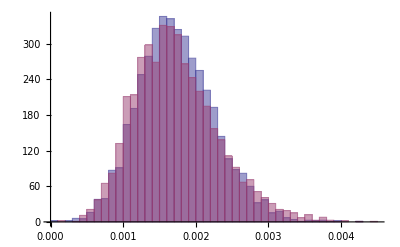

```mathematica
Histogram[{res[[;;,3]],resh[[;;,3]]},"Knuth",PlotRange->All]
```

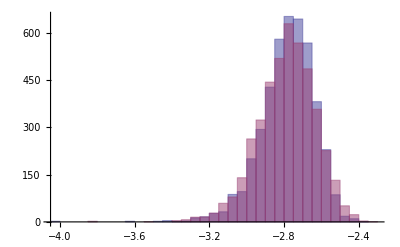

```mathematica
Histogram[{Log[10,res[[;;,3]]],Log[10,resh[[;;,3]]]},"Knuth",PlotRange->All]
```

```mathematica
sortres=Sort[res,#1[[3]]>#2[[3]]&];sortresh=Sort[resh,#1[[3]]>#2[[3]]&];
```

```mathematica
sortres[[1;;20,;;]]//MF
```

(68 | 89 | 0.00428197
88 | 89 | 0.00392101
59 | 90 | 0.00391304
32 | 89 | 0.00383417
59 | 89 | 0.00378546
89 | 90 | 0.00376354
64 | 89 | 0.0037567
72 | 89 | 0.00361801
6 | 57 | 0.00361688
61 | 88 | 0.00359064
69 | 89 | 0.00356539
9 | 58 | 0.00352329
32 | 66 | 0.00349298
34 | 89 | 0.00337852
46 | 90 | 0.00337457
31 | 66 | 0.00331328
6 | 53 | 0.0033014
6 | 21 | 0.00327939
42 | 68 | 0.00327784
9 | 38 | 0.00327634)

```mathematica
sortresh[[1;;20,;;]]//MF
```

(35 | 91 | 0.00448058
11 | 29 | 0.00428783
62 | 85 | 0.00403889
4 | 86 | 0.00402846
2 | 69 | 0.00397398
38 | 89 | 0.003862
9 | 92 | 0.00386144
81 | 83 | 0.00385724
38 | 84 | 0.00378124
7 | 90 | 0.00377196
83 | 90 | 0.00375366
15 | 90 | 0.0037463
7 | 83 | 0.00374476
33 | 38 | 0.00374082
86 | 92 | 0.00373145
66 | 82 | 0.00370156
3 | 10 | 0.00369783
36 | 91 | 0.00364435
30 | 80 | 0.00364293
8 | 87 | 0.00358121)

```mathematica
94*93/2
```

4371

```mathematica
tab=Table[Tally[Flatten@sortres[[1;;i,1;;2]]],{i,60}];
```

```mathematica
tab[[10]]
```

{{68,1},{89,7},{88,2},{59,2},{90,2},{32,1},{64,1},{72,1},{6,1},{57,1},{61,1}}

```mathematica
tabh=Table[Tally[Flatten@sortresh[[1;;i,1;;2]]],{i,60}];
```

```mathematica
tabh[[10]]
```

{{84,1},{94,1},{45,1},{80,1},{9,1},{83,1},{51,1},{89,1},{6,1},{92,2},{60,1},{32,1},{93,1},{12,1},{35,1},{21,1},{72,1},{44,1},{76,1}}

```mathematica
tabh[[10]]
```

{{35,1},{91,1},{11,1},{29,1},{62,1},{85,1},{4,1},{86,1},{2,1},{69,1},{38,2},{89,1},{9,1},{92,1},{81,1},{83,1},{84,1},{7,1},{90,1}}

```mathematica
tab2=Table[Union[Flatten@sortres[[1;;i,1;;2]]],{i,60}];
```

```mathematica
best={};i=1;While[Length@best<4,best=Union[Flatten@sortres[[1;;i,1;;2]]];i=i+1];
```

```mathematica
best
```

{59,68,88,89,90}

```mathematica
best2={};i=1;While[sortres[[i,3]]>0.003,best2=Union[Flatten@sortres[[1;;i,1;;2]]];i=i+1];Length@best2
```

45

```mathematica
best2
```

{3,6,9,16,17,20,21,26,30,31,32,33,34,35,38,42,46,51,52,53,55,57,58,59,61,64,66,67,68,69,70,72,75,77,78,79,82,83,85,88,89,90,91,92,93}

```mathematica
sin=Flatten@Import["results_single.csv"];sinh=Flatten@Import["results_single_shuffle.csv"];
```

```mathematica
Dimensions[sin]
```

{94}

```mathematica
BarChart
```

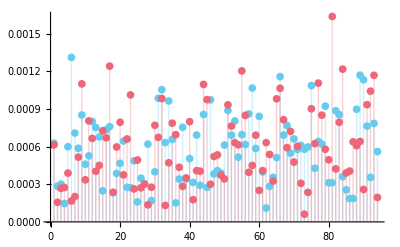

```mathematica
ListPlot[{sin,sinh},PlotRange->All,Filling->Axis]
```

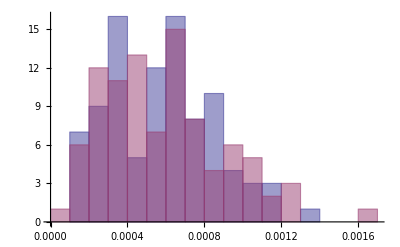

```mathematica
Histogram[{sin,sinh},"Knuth",PlotRange->All]
```

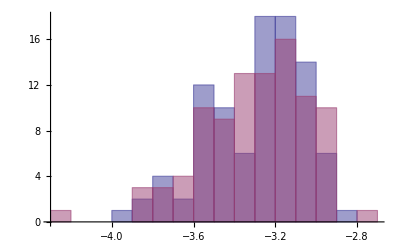

```mathematica
Histogram[{Log[10,sin],Log[10,sinh]},"Knuth",PlotRange->All]
```

```mathematica
(sortsin={Ordering[sin,Length[sin],Greater],Sort[sin,Greater]})//T//MF
```

(6 | 0.00131027
89 | 0.00116852
66 | 0.00115693
90 | 0.00113193
75 | 0.00108549
58 | 0.00106609
32 | 0.00105305
31 | 0.000984462
46 | 0.000972142
34 | 0.000963016
79 | 0.000921927
88 | 0.000897444
51 | 0.000887513
82 | 0.000885338
57 | 0.00086006
44 | 0.000855502
83 | 0.000853903
9 | 0.000851118
60 | 0.000840379
53 | 0.000804193
12 | 0.000800258
93 | 0.000784203
68 | 0.000767841
91 | 0.00076261
17 | 0.000759066
38 | 0.000753694
13 | 0.000751556
16 | 0.000733536
7 | 0.000707674
55 | 0.000695119
42 | 0.000691679
52 | 0.000691242
67 | 0.000691236
14 | 0.000676267
70 | 0.000660921
35 | 0.000656793
21 | 0.000644039
77 | 0.000640793
33 | 0.000632158
1 | 0.000626947
78 | 0.000619935
28 | 0.000619372
56 | 0.000616334
50 | 0.000612095
72 | 0.000609122
5 | 0.00059906
74 | 0.000596532
8 | 0.000586037
59 | 0.000585208
73 | 0.000578946
71 | 0.000576972
94 | 0.000559832
69 | 0.000547758
11 | 0.000525723
54 | 0.000515167
65 | 0.000512055
40 | 0.000503994
24 | 0.000486518
20 | 0.000466659
10 | 0.000459652
76 | 0.000426999
48 | 0.000408192
30 | 0.000399139
61 | 0.000397563
49 | 0.000388632
19 | 0.00038584
47 | 0.000381911
84 | 0.000359279
64 | 0.000355055
92 | 0.000354519
26 | 0.000348427
37 | 0.00034136
39 | 0.000340822
41 | 0.000314223
81 | 0.000311884
80 | 0.000311884
27 | 0.000305597
3 | 0.000300882
43 | 0.000291741
2 | 0.000284827
63 | 0.000282566
22 | 0.000275119
45 | 0.000274709
23 | 0.000272707
85 | 0.000255111
15 | 0.000247417
18 | 0.000231691
87 | 0.000185875
86 | 0.000185875
29 | 0.000169322
25 | 0.000159272
36 | 0.000150975
4 | 0.000146328
62 | 0.000110429)

```mathematica
Sort[
```